```mathematica
ClearAll["Global`*"]
QWP={{1,0},{0,-I}}
HWP={{1,0},{0,-1}}
R={{Cos[t],-Sin[t]},{Sin[t],Cos[t]}}
R1=R/.t->q
R2=R/.t->-q
```

{{1,0},{0,-ⅈ}}

{{1,0},{0,-1}}

{{Cos[t],-Sin[t]},{Sin[t],Cos[t]}}

{{Cos[q],-Sin[q]},{Sin[q],Cos[q]}}

{{Cos[q],Sin[q]},{-Sin[q],Cos[q]}}

```mathematica
HWP1=R1.HWP.R2
```

{{Cos[q]^2-Sin[q]^2,2 Cos[q] Sin[q]},{2 Cos[q] Sin[q],-Cos[q]^2+Sin[q]^2}}

```mathematica
HWP2=R1.HWP.R2/.q->p
```

{{Cos[p]^2-Sin[p]^2,2 Cos[p] Sin[p]},{2 Cos[p] Sin[p],-Cos[p]^2+Sin[p]^2}}

```mathematica
Mk={{1+b,0},{0,1}}
```

{{1+b,0},{0,1}}

```mathematica
NM={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
HWP11=HWP1/.q->t/2
```

{{Cos[t/2]^2-Sin[t/2]^2,2 Cos[t/2] Sin[t/2]},{2 Cos[t/2] Sin[t/2],-Cos[t/2]^2+Sin[t/2]^2}}

```mathematica
Outgoing=HWP2.NM.HWP11.{{0},{1}}
```

{{2 Cos[t/2] (Cos[p]^2-Sin[p]^2) Sin[t/2]+2 Cos[p] Sin[p] (-Cos[t/2]^2+Sin[t/2]^2)},{4 Cos[p] Cos[t/2] Sin[p] Sin[t/2]+(-Cos[p]^2+Sin[p]^2) (-Cos[t/2]^2+Sin[t/2]^2)}}

```mathematica
Es=Part[Outgoing,1]
```

{2 Cos[t/2] (Cos[p]^2-Sin[p]^2) Sin[t/2]+2 Cos[p] Sin[p] (-Cos[t/2]^2+Sin[t/2]^2)}

```mathematica
Ep=Part[Outgoing,2]
```

{4 Cos[p] Cos[t/2] Sin[p] Sin[t/2]+(-Cos[p]^2+Sin[p]^2) (-Cos[t/2]^2+Sin[t/2]^2)}

```mathematica
Es^2-Ep^2
```

{(2 Cos[t/2] (Cos[p]^2-Sin[p]^2) Sin[t/2]+2 Cos[p] Sin[p] (-Cos[t/2]^2+Sin[t/2]^2))^2-(4 Cos[p] Cos[t/2] Sin[p] Sin[t/2]+(-Cos[p]^2+Sin[p]^2) (-Cos[t/2]^2+Sin[t/2]^2))^2}

```mathematica
Simplify[%] (* p=q+pi/8 is the angle of HWP2 to balance*)
```

{-Cos[4 p-2 t]}

```mathematica
a=Pi/8+t/2
```

π/8+t/2

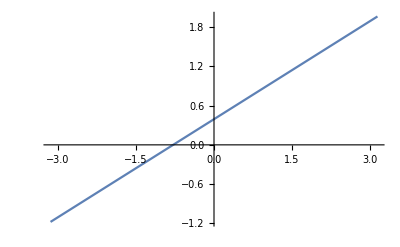

```mathematica
Plot[a,{t,-Pi,Pi}]
```

```mathematica
HWP12=HWP2/.p->a
Simplify[%]
```

{{Cos[π/8+t/2]^2-Sin[π/8+t/2]^2,2 Cos[π/8+t/2] Sin[π/8+t/2]},{2 Cos[π/8+t/2] Sin[π/8+t/2],-Cos[π/8+t/2]^2+Sin[π/8+t/2]^2}}

{{(Cos[t]-Sin[t])/(√2),Sin[π/4+t]},{Sin[π/4+t],(-Cos[t]+Sin[t])/(√2)}}

```mathematica
outgoing2=HWP12.Mk.HWP11.{{0},{1}}
```

{{2 (1+b) Cos[t/2] (Cos[π/8+t/2]^2-Sin[π/8+t/2]^2) Sin[t/2]+2 Cos[π/8+t/2] Sin[π/8+t/2] (-Cos[t/2]^2+Sin[t/2]^2)},{4 (1+b) Cos[π/8+t/2] Cos[t/2] Sin[π/8+t/2] Sin[t/2]+(-Cos[π/8+t/2]^2+Sin[π/8+t/2]^2) (-Cos[t/2]^2+Sin[t/2]^2)}}

```mathematica
Simplify[%]
```

{{(1/4-ⅈ/4) (-1)^(1/4) (-2-b+b Cos[2 t]+b Sin[2 t])},{(1/4+ⅈ/4) (-1)^(3/4) (-2-b+b Cos[2 t]-b Sin[2 t])}}

```mathematica
Ess=Part[outgoing2,1]/.t->Pi/4
Epp=Part[outgoing2,2]/.t->Pi/4
```

```mathematica
KR=Ess*Conjugate[Ess]-Epp*Conjugate[Epp]/.b->x+I y/.t->Pi/4
```

{-4 (1+x+ⅈ y) (1+Conjugate[x]-ⅈ Conjugate[y]) Cos[π/8]^2 Sin[π/8]^2+(-Cos[π/8]^2+Sin[π/8]^2)^2}

```mathematica
Simplify[%]
```

{1/2 (-x-ⅈ y-(1+x+ⅈ y) Conjugate[x]+ⅈ (1+x+ⅈ y) Conjugate[y])}

```mathematica
KRplot=Simplify[%,Element[b,Reals]&&Element[t,Reals]]
```

{1/2 (-x-ⅈ y-(1+x+ⅈ y) Conjugate[x]+ⅈ (1+x+ⅈ y) Conjugate[y])}

```mathematica
Plot[KRplot*1^2/.b->0.1,{t,-Pi,Pi},GridLines->{{-Pi,-3Pi/4,-Pi/2,-Pi/4,Pi/4,Pi/2,3Pi/4,Pi},{}}]
```

-Graphics-

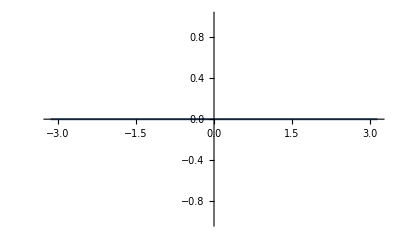

```mathematica
Needs["NumericalCalculus`"]
ND[KRplot,b,0.1];
Plot[%,{t,-Pi,Pi}]
```

```mathematica
M3={{1,d},{-d,1}};
outgoing3=HWP12.M3.HWP11.{{0},{1}};
```

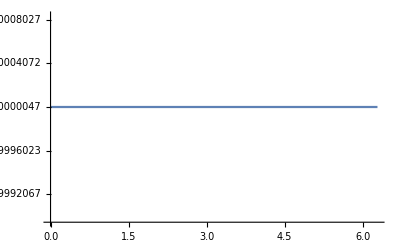

```mathematica
Es3=Part[outgoing3,1];
Ep3=Part[outgoing3,2];
KR3=Es3*Conjugate[Es3]-Ep3*Conjugate[Ep3];
Plot[KR3/.d->0.03+0.03 I,{t,0,2Pi}]
```